# Examples and tests for FFmpeg

```mathematica
Quit[];
```

```mathematica
Import @ FileNameJoin @ {NotebookDirectory[] , "FFmpeg.m"}
```

## Example Use

```mathematica
FFImport["http://er.jsc.nasa.gov/seh/jfkrice.avi", {"Frames", 2}]
```

-Graphics-

```mathematica
FFImport["http://er.jsc.nasa.gov/seh/jfkrice.avi", {"Frames", Range[2,10]}] //Short
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FFmpeg[]
```

ffmpeg was found and is functional

## Tests

```mathematica
vid = "D:\\25\\1\\video_0.avi";
```

#### Testing input for the functions

```mathematica
elements = {"Frames", 1};

Switch[ elements, 
{"Frames",_Integer}, "one number",
{"Frames",{_Integer,_}}, "vector",
{_String, _}, "Command",
_, "not"
]
```

one number

#### Test if frame seeker gets the right frame

```mathematica
CompateImports[frame_,offset_:0]:=Module[{img0,img1 },
img0 =FFImport[vid, {"Frames",{frame+offset}}][[1]];
img1 = FFImport[vid, {"Frames",{frame}, True}][[1]];
ImageDifference[img0,img1]
]
```

```mathematica
cc = Table[ Total[ImageData@CompateImports[300, i], 3] , {i,Range[-5,5]}]
```

{78329.6,78510.3,78395.,78228.4,78089.7,77615.4,78229.6,78347.3,78531.1,78758.4,78843.9}

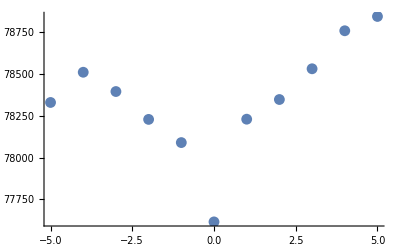

```mathematica
ListPlot[ Transpose@ { Range[-5,5], cc} ]
```

```mathematica
CompateImports[57851, 0]//ImageAdjust
```

-Graphics-

#### Test take multiple frames

```mathematica
setImg0 = FFImport[vid, {"Frames",{1,2,10,1000,10000, 10001}}];
```

```mathematica
setImg1 = Import[vid, {"Frames",{1,2,10,1000,10000, 10001}}];

ImageDifference[#⟦1⟧, #⟦2⟧]&/@(Transpose@ {setImg0, setImg1})
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Methematica’s default method imports not the right frame - seems to be the same consecutive frame. Periodicity for test video - 15 frames.

#### Test speed

```mathematica
no = 5;
start = 40000;

"ffmpeg"-> AbsoluteTiming[FFImport[vid, {"Frames",Range[start,no+start]}]]⟦1⟧

"ffmpeg new"-> AbsoluteTiming[FFImport[vid, {"Frames",Range[start,no+start], True}]]⟦1⟧

"QuickTime"-> AbsoluteTiming[Import[vid, {"Frames",Range[start,no+start]}]]⟦1⟧
```

ffmpeg→50.45705

experimental frame grabber - ffmpeg

ffmpeg new→440.09701

QuickTime→0.83108

Seeking is slow! No fast way of seeking test video was found.